# Symbolic computation for quantum circuits

Compute quantum circuit operations symbolically

## Example Content

Introductory paragraph about the example.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Define BooleanOracle circuit, for a Boolean function:

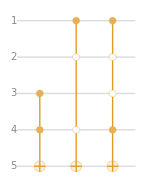

```mathematica
qc=QuantumCircuitOperator[{"BooleanOracle",a&&!b||c&&d}];
qc["Diagram"]
```

Transform a superposition (only first term is the solution of above Boolean function) using corresponding BooleanOracle circuit:

```mathematica
qc[α QuantumState["11110"]+β QuantumState["11010"]]//TraditionalForm
```

β 11010+α 11111

Define a Multiplexer using symbolic rotations:

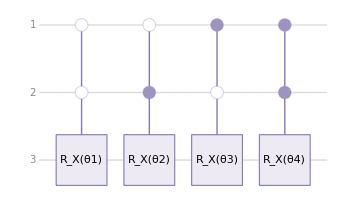

```mathematica
qc=QuantumCircuitOperator[{"Multiplexer",{"RX",θ1},{"RX",θ2},{"RX",θ3},{"RX",θ4}}];
qc["Diagram"]
```

Represent the corresponding matrix:

```mathematica
FullSimplify[Normal[qc["Matrix"]]]//MatrixForm
```

(Cos[θ1/2] | -ⅈ Sin[θ1/2] | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ Sin[θ1/2] | Cos[θ1/2] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[θ2/2] | -ⅈ Sin[θ2/2] | 0 | 0 | 0 | 0
0 | 0 | -ⅈ Sin[θ2/2] | Cos[θ2/2] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[θ3/2] | -ⅈ Sin[θ3/2] | 0 | 0
0 | 0 | 0 | 0 | -ⅈ Sin[θ3/2] | Cos[θ3/2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Cos[θ4/2] | -ⅈ Sin[θ4/2]
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ Sin[θ4/2] | Cos[θ4/2])

Define a circuit, with symbolic quantum channel:

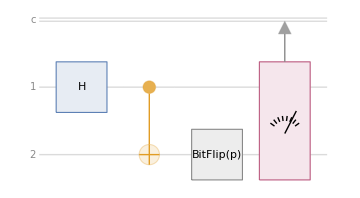

```mathematica
qc=QuantumCircuitOperator[{"H","CNOT",QuantumChannel[{"BitFlip",p},{2}],{1,2}}];
qc["Diagram"]
```

Find quantum probabilities:

```mathematica
FullSimplify[#,Assumptions->{0<=p<=1}]&/@qc[]["Probabilities"]
```

<|00→1-p,01→p,10→0,11→0|>

Create a list of operators using a Hamiltonian as 3-qubits interacting based on Ising model H=X_1 X_2+X_2 X_3:
4th order, only 1 step:

```mathematica
QuantumCircuitOperator[{"Trotterization",{QuantumOperator["X",{1,2}],QuantumOperator["X",{2,3}]},4,1,t}]//QuantumShortcut
```

{{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,(1-4/(4-2^(2/3))) t,X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)},{R,t/(4-2^(2/3)),X^(⊗2)}}

Phase estimation circuit of a symbolic unitary:

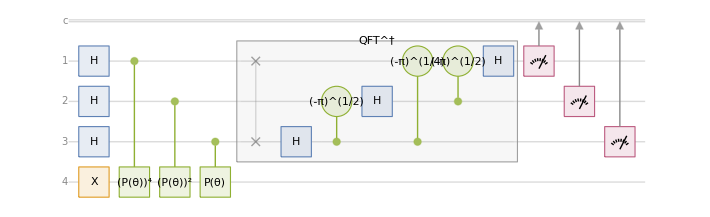

```mathematica
QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator[{"P",θ}],3}]["Diagram"]
```

Composition of circuits

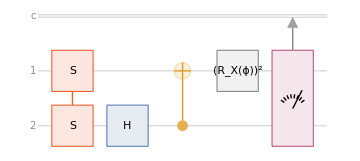

```mathematica
qc=QuantumMeasurementOperator[{1,2}]@*(QuantumOperator[{"RX",ϕ}]^2)@*QuantumCircuitOperator["Magic"];
qc["Diagram"]
```

Calculate quantum probabilities:

```mathematica
FullSimplify[#,Assumptions->{ϕ∈Reals}]&/@qc[]["Probabilities"]
```

<|00→Cos[ϕ]^2/2,01→Sin[ϕ]^2/2,10→Sin[ϕ]^2/2,11→Cos[ϕ]^2/2|>

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

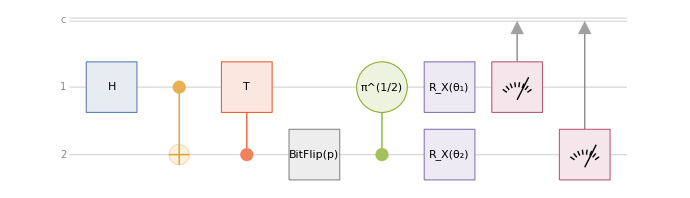

```mathematica
QuantumCircuitOperator[{"H","CNOT","CT"->{2,1},QuantumChannel[{"BitFlip",p},{2}],{"C",2,{2}},{"RX",Subscript[θ, 1]},{"RX",Subscript[θ, 2]}->2,{1},{2}}]["Diagram"]
```

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum circuit

Symbolic computation

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.